Using the τ non-dimensionalization of the hydrodynamic model, analytically solve for critical activity with respect to γ̇ under the assumption that k=l=0

```mathematica
Solve[(τ a)/η==((1+σ τ)^2/(γd τ)+γd τ)/((λ(1+σ τ))/(γd τ(1+γd^2 τ^2))-(γd λ τ)/(1 + γd^2 τ^2)),σ]
```

{{σ→(-2 η τ+a λ τ^2-2 γd^2 η τ^3-τ^2 √(-4 γd^2 η^2+a^2 λ^2-4 a γd^2 η λ τ-8 γd^4 η^2 τ^2-4 a γd^4 η λ τ^3-4 γd^6 η^2 τ^4))/(2 (η τ^2+γd^2 η τ^4))},{σ→(-2 η τ+a λ τ^2-2 γd^2 η τ^3+τ^2 √(-4 γd^2 η^2+a^2 λ^2-4 a γd^2 η λ τ-8 γd^4 η^2 τ^2-4 a γd^4 η λ τ^3-4 γd^6 η^2 τ^4))/(2 (η τ^2+γd^2 η τ^4))}}

```mathematica
Subscript[σ, 1]=(-2 η τ+a λ τ^2-2 γd^2 η τ^3-τ^2 √(-4 γd^2 η^2+a^2 λ^2-4 a γd^2 η λ τ-8 γd^4 η^2 τ^2-4 a γd^4 η λ τ^3-4 γd^6 η^2 τ^4))/(2 (η τ^2+γd^2 η τ^4))/.{η->1,τ->1,λ->1};
Subscript[σ, 2]=(-2 η τ+a λ τ^2-2 γd^2 η τ^3+τ^2 √(-4 γd^2 η^2+a^2 λ^2-4 a γd^2 η λ τ-8 γd^4 η^2 τ^2-4 a γd^4 η λ τ^3-4 γd^6 η^2 τ^4))/(2 (η τ^2+γd^2 η τ^4))/.{η->1,τ->1,λ->1};
```

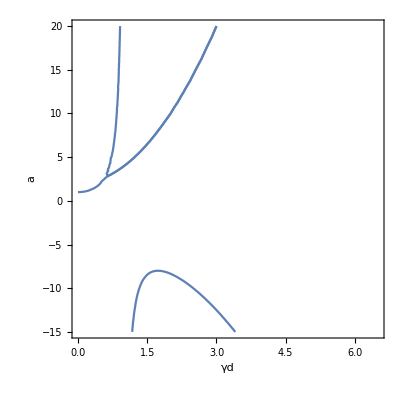

```mathematica
p1=ContourPlot[Re[Subscript[σ, 1]]==0,{γd,0,6.5}, {a,-15,20},AxesLabel->Automatic];
p2=ContourPlot[Re[Subscript[σ, 2]]==0,{γd,0,6.5}, {a,-15,20},AxesLabel->Automatic];
Show[p1,p2]
```

```mathematica
There is a clear qualitative and quantitative difference between this analytic result and the computational result...1) Asymptote at γd=1 for both branches 2) the critical activity for γd =0 is 1 instead of ~0.6 as seen in computational studies.
```

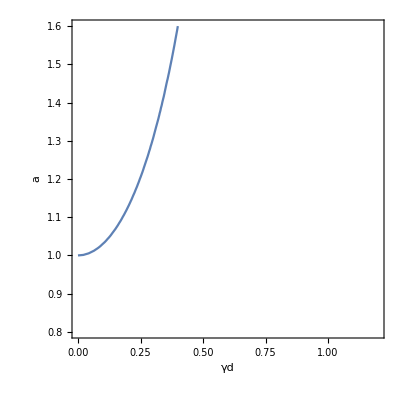

```mathematica
ContourPlot[Subscript[σ, 2]==0,{γd,0,1.2}, {a,0.8,1.6},AxesLabel->Automatic]
```

```mathematica
Subscript[σ, 1]
```

(-2+a-2 γd^2-√(a^2-4 γd^2-4 a γd^2-8 γd^4-4 a γd^4-4 γd^6))/(2 (1+γd^2))

```mathematica
Subscript[σ, 2]
```

(-2+a-2 γd^2+√(a^2-4 γd^2-4 a γd^2-8 γd^4-4 a γd^4-4 γd^6))/(2 (1+γd^2))